Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

t11r1: {{10.9702,2.22824},{1.25982,-0.836961}}

t11t12: {{10.9702,2.22824},{11.0465,2.11436}}

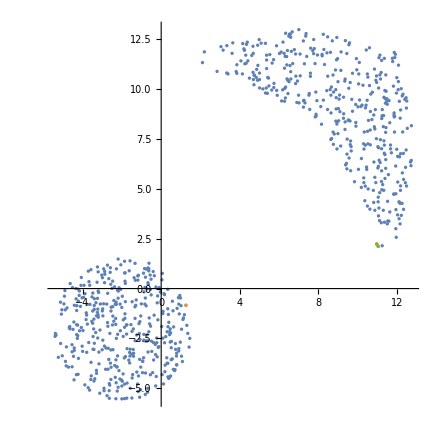

t21r2: {{11.0465,2.11436},{1.25982,-0.836961}}

t21t22: {{11.0465,2.11436},{10.9702,2.22824}}

t21t23: {{11.0465,2.11436},{11.2486,2.14568}}

t21t24: {{11.0465,2.11436},{10.9702,2.22824}}

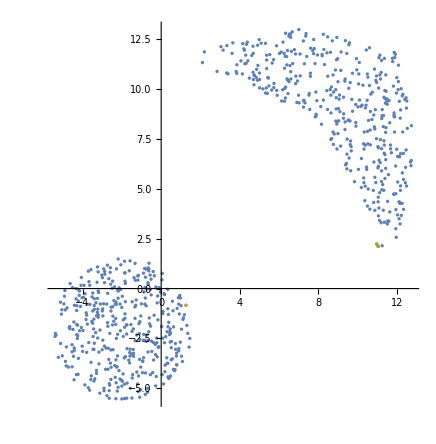

Sink: {{0.680925,-4.10957}}

t31r3: {{11.0465,2.11436},{1.25982,-0.836961}}

t31t32: {{11.0465,2.11436},{10.9702,2.22824}}

t31t33: {{11.0465,2.11436},{11.2486,2.14568}}

t31t34: {{11.0465,2.11436},{10.9702,2.22824}}

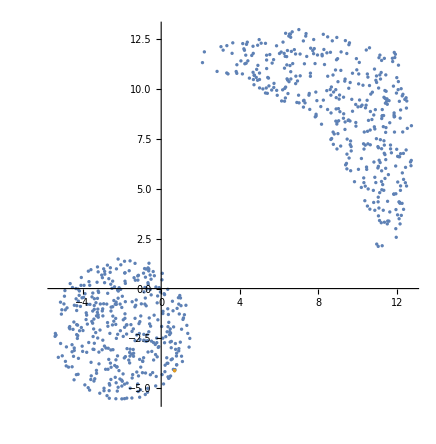

t21 is the same as t11 in: 0 of 1 tests.

t31 is the same as t11 in: 0 of 1 tests.

Histogram distancet21r2 - distancet11r1

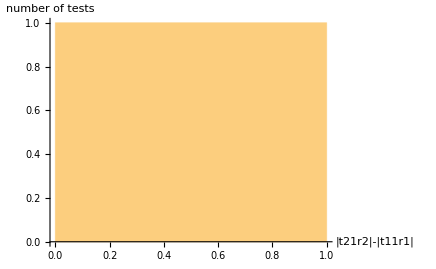

Histogram distancet31r3 - distancet11r1

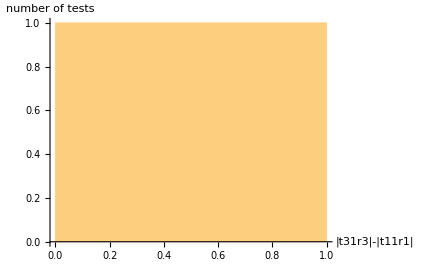

Average distance t11 - > r1 = 10.1827

Average distance t21 - > r2 = 10.222

Average distance t31 - > r3 = 10.222

Average distance t12 - > r1 = 10.222

Average distance t22 - > r2 = 10.1827

Average distance t23 - > r2 = 10.4246

Average distance t24 - > r2 = 10.1827

Average distance t25 - > r2 = 15.2872

Average distance t32 - > r3 = 10.1827

Average distance t33 - > r3 = 10.4246

Average distance t34 - > r3 = 10.1827

Average distance t11 - > t12 = 0.137093

Average distance t21 - > t22 = 0.137093

Average distance t21 - > t23 = 0.204506

Average distance t21 - > t24 = 0.137093

Average distance t21 - > t25 = 8.85615

Average distance t31 - > t32 = 0.137093

Average distance t31 - > t33 = 0.204506

Average distance t31 - > t34 = 0.137093

```mathematica
(*Global Variables*)
numOfPoints = 400;
numOfTests = 1;

sink;
t11r1; (*NEAREST points of two regions, t11 - from all points, r1 - from all points*)
t11t12; 
t21r2;(*nearest points if, t21 - from ConvexHull, r2 - from all points*)
t21t22;
t21t23;
t21t24;
t21t25;
t31r3; (*nearest points if, t31 - from ConvexHull and is nearest to Sink, r3 - from all points*)
t31t32;
t31t33;
t31t34;

t21EqualsTot11 = 0;
t31EqualsTot11 = 0;

(*distances transmitter -> receiver*)
distancet11r1 = 0.0;
distancet12r1 = 0.0;
distancet21r2 = 0.0;
distancet22r2 = 0.0;
distancet23r2 = 0.0;
distancet24r2 = 0.0;
distancet25r2 = 0.0;
distancet31r3 = 0.0;
distancet32r3 = 0.0;
distancet33r3 = 0.0;
distancet34r3 = 0.0;

(*distances transmitter -> transmitter*)
distancet11t12 = 0.0;
distancet21t22 = 0.0;
distancet21t23 = 0.0;
distancet21t24 = 0.0;
distancet21t25 = 0.0;
distancet31t32 = 0.0;
distancet31t33 = 0.0;
distancet31t34 = 0.0;

distDiff1={}; (* list of: distancet21r2 - distancet11r1, without zeros*)
distDiff2={};(* list of: distancet31r3 - distancet11r1, without zeros*)

(*Distributin function for generating point on given region
zdroj: http://mathematica.stackexchange.com/questions/57938/how-to-generate-random-points-in-a-region
*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*(*Initialize of two CIRCLE regions*)
region1 = DiscretizeRegion@Disk[{5, 5}, 3.568];
region2 = DiscretizeRegion@Disk[{13,13}, 3.568];*)

(*(*Initialize of two RECTANGLE regions*)
region1 = DiscretizeRegion@Rectangle[{0,1},{10,5}];
region2 = DiscretizeRegion@Rectangle[{2,7},{12,11}];*)

Do[
Module[{},
(*Initialize of two POLYGON regions*)
region2 = DiscretizeRegion@Disk[{-2, -2}, 3.568];
region1 = DiscretizeRegion@Polygon[{{12,2},{11,2},{10.5,4}, {7.5,9.5}, {9.5,7.5}, {4,10.5},{2,11},{2,12}, {7,13},{12, 12},{13,7}}];

(*Filll areas with points*)
pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];
area = Join[pts1, pts2];

(*(*Export data to file*)
DumpSave["file.mx",area];*)

(*Initialize sink*)
sink = RandomSample[pts2, 1];

(*Exctract points on convex hull - both regions*)
ch1Region = RegionBoundary[ConvexHullMesh[pts1]];
ch2Region = RegionBoundary[ConvexHullMesh[pts2]];
ch1pts = pts1;
cutConvexHull1[x_]=If[RegionMember[ch1Region,ch1pts[[x]]],(*Print[arrayOneConvexHull[[x]]]*), 
ch1pts = Delete[ch1pts, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];
ch2pts  = pts2;
cutConvexHull2[x_]=If[RegionMember[ch2Region,ch2pts [[x]]],(*Print[arrayTwoConvexHull[[x]]]*), 
ch2pts  = Delete[ch2pts , x]];
For[i=numOfPoints, i>0, i--, cutConvexHull2[i]];

(*
==========================================FINDING FIRST TRANSMITTER==========================================
*)

(*Calculate NEAREST points of two regions
t11 - from all points
r1 - from all points*)
r = Nearest[pts1];
d = Flatten[r/@pts2,1];
t11r1 = Flatten[Transpose[{d[[#]],pts2[[#]]}]&@Ordering[Norm/@(d-pts2),1],1];

(*Calculate nearest points if
t21 - from ConvexHull 
r2 - from all points*)
f = Nearest[ch1pts];
c=Flatten[f/@pts2,1];
t21r2 = Flatten[Transpose[{c[[#]],pts2[[#]]}]&@Ordering[Norm/@(c-pts2),1],1];

(*Calculate nearest points if
t31 - from ConvexHull and is nearest to Sink
r3 - from all points*)
f = Nearest[ch1pts];
c=Flatten[f/@sink,1];
t31sink = Flatten[Transpose[{c[[#]],sink[[#]]}]&@Ordering[Norm/@(c-sink),1],1];
r3 = Nearest[pts2, t31sink[[1]]];
t31r3 = Join[Partition[t31sink[[1]],2, 1], r3];

(*
==========================================FINDING SECOND TRANSMITTER==========================================
*)

(*t12 == Closest point to t11*) 
t11t12 = Nearest[pts1,t11r1[[1]],{2,4}]; 

(*t22 == Closest point to t21*) 
t21t22 = Nearest[pts1,t21r2[[1]],{2,4}]; 
(*t23 == closest point to t21, looking only on convex hull*)
t21t23 = Nearest[ch1pts,t21r2[[1]],{2,8}]; 
(*t24 == Delete t21 from Convex Hull, recalculate it and find the second point the same way as the first one => nearest to all points*)
pr1 = Position[pts1, t21r2[[1]]];
pts1r1 = Delete[pts1, pr1];
ch1Regionr1 = RegionBoundary[ConvexHullMesh[pts1r1]];
ch1ptsr1 = pts1r1;
cutConvexHull1r1[x_]=If[RegionMember[ch1Regionr1,ch1ptsr1[[x]]],(*Print[ch1ptsr1[[x]]]*), 
ch1ptsr1 = Delete[ch1ptsr1, x]];
For[i=numOfPoints-1, i>0, i--, cutConvexHull1r1[i]];
f = Nearest[ch1ptsr1];
c=Flatten[f/@pts2,1];
t24r22 = Flatten[Transpose[{c[[#]],pts2[[#]]}]&@Ordering[Norm/@(c-pts2),1],1];
t21t24 = Join[Partition[t21r2[[1]],2, 1], Partition[t24r22[[1]],2, 1]];

(*t25 == Delete t21 from Convex Hull, recalculate it and find the second point nearest to r2*)
pr3 = Position[pts1, t21r2[[1]]];
pts1r3 = Delete[pts1, pr3];
ch1Regionr3 = RegionBoundary[ConvexHullMesh[pts1r3]];
ch1ptsr3 = pts1r3;
cutConvexHull1r3[x_]=If[RegionMember[ch1Regionr3,ch1ptsr3[[x]]],(*Print[ch1ptsr1[[x]]]*), 
ch1ptsr3 = Delete[ch1ptsr3, x]];
For[i=numOfPoints-1, i>0, i--, cutConvexHull1r3[i]];
t25 = Flatten[Nearest[ch1ptsr3, t21r2[[2]]],1];
t21t25 = Join[Partition[t21r2[[1]],2, 1], t25];

(*t32 == Closest point to t31*) 
t31t32 = Nearest[pts1,t31r3[[1]],{2,4}]; 
(*t33 == closest point to t31, looking only on convex hull*)
t31t33 = Nearest[ch1pts,t31r3[[1]],{2,8}]; 
(*t34 == Delete t31 from Convex Hull, recalculate it and find the second point the same way as the first one => nearest to sink*)
pr2 = Position[pts1, t31r3[[1]]];
pts1r2 = Delete[pts1, pr2];
ch1Regionr2 = RegionBoundary[ConvexHullMesh[pts1r2]];
ch1ptsr2 = pts1r2;
cutConvexHull1r2[x_]=If[RegionMember[ch1Regionr2,ch1ptsr2[[x]]],(*Print[ch1ptsr2[[x]]]*), 
ch1ptsr2 = Delete[ch1ptsr2, x]];
For[i=numOfPoints-1, i>0, i--, cutConvexHull1r2[i]];
t34 = Flatten[Nearest[ch1ptsr2, sink],1];
t31t34 = Join[Partition[t31r3[[1]],2, 1], t34];

(*
========================================TESTING AND COMPARING RESULTS========================================
*)

If[t21r2[[1]]== t11r1[[1]],
t21EqualsTot11++;
,];

If[t31r3[[1]]== t11r1[[1]],
t31EqualsTot11++;
,];

distancet11r1 += EuclideanDistance[t11r1[[1]], t11r1[[2]]];
distancet12r1 += EuclideanDistance[t11t12[[2]], t11r1[[2]]];
distancet21r2 += EuclideanDistance[t21r2[[1]], t21r2[[2]]];
distancet22r2 += EuclideanDistance[t21t22[[2]], t21r2[[2]]];
distancet23r2 += EuclideanDistance[t21t23[[2]], t21r2[[2]]];
distancet24r2 += EuclideanDistance[t21t24[[2]], t21r2[[2]]];
distancet25r2 += EuclideanDistance[t21t25[[2]], t21r2[[2]]];
distancet31r3 += EuclideanDistance[t31r3[[1]], t31r3[[2]]];
distancet32r3 += EuclideanDistance[t31t32[[2]], t31r3[[2]]];
distancet33r3 += EuclideanDistance[t31t33[[2]], t31r3[[2]]];
distancet34r3 += EuclideanDistance[t31t34[[2]], t31r3[[2]]];

distancet11t12 += EuclideanDistance[t11t12[[1]], t11t12[[2]]];
distancet21t22 += EuclideanDistance[t21t22[[1]], t21t22[[2]]];
distancet21t23 += EuclideanDistance[t21t23[[1]], t21t23[[2]]];
distancet21t24 += EuclideanDistance[t21t24[[1]], t21t24[[2]]];
distancet21t25 += EuclideanDistance[t21t25[[1]], t21t25[[2]]];
distancet31t32 += EuclideanDistance[t31t32[[1]], t31t32[[2]]];
distancet31t33 += EuclideanDistance[t31t33[[1]], t31t33[[2]]];
distancet31t34 += EuclideanDistance[t31t34[[1]], t31t34[[2]]];

If[EuclideanDistance[t21r2[[1]], t21r2[[2]]] - EuclideanDistance[t11r1[[1]], t11r1[[2]]] == 0., 
,distDiff1= Append[distDiff1, EuclideanDistance[t21r2[[1]], t21r2[[2]]] - EuclideanDistance[t11r1[[1]], t11r1[[2]]]]
];
If[EuclideanDistance[t31r3[[1]], t31r3[[2]]] - EuclideanDistance[t11r1[[1]], t11r1[[2]]] == 0.,
,distDiff2= Append[distDiff2, EuclideanDistance[t31r3[[1]], t31r3[[2]]] - EuclideanDistance[t11r1[[1]], t11r1[[2]]]]
];

],{numOfTests}]

(*
========================================PRESENTING OF RESULTS========================================
*)

Print["t11r1: ", t11r1]
Print["t11t12: ", t11t12]
ListPlot[{area, t11r1, t11t12}, AspectRatio->Automatic]

Print["t21r2: ", t21r2]
Print["t21t22: ", t21t22]
Print["t21t23: ", t21t23]
Print["t21t24: ", t21t24]
ListPlot[{area, t21r2, t21t22}, AspectRatio->Automatic]

Print["Sink: ", sink]
Print["t31r3: ", t31r3]
Print["t31t32: ", t31t32]
Print["t31t33: ", t31t33]
Print["t31t34: ", t31t34]
ListPlot[{area, sink}, AspectRatio->Automatic]

Print["t21 is the same as t11 in: ", t21EqualsTot11, " of ", numOfTests, " tests. " ]
Print["t31 is the same as t11 in: ", t31EqualsTot11, " of ", numOfTests, " tests. " ]

Print["Histogram distancet21r2 - distancet11r1"]
Histogram[distDiff1, AxesLabel->{"|t21r2|-|t11r1|", number of tests}]
Print["Histogram distancet31r3 - distancet11r1"]
Histogram[distDiff2, AxesLabel->{"|t31r3|-|t11r1|", number of tests}]

Print["Average distance t11 - > r1 = ", distancet11r1/numOfTests]
Print["Average distance t21 - > r2 = ", distancet21r2/numOfTests]
Print["Average distance t31 - > r3 = ", distancet31r3/numOfTests]
Print[""]
Print["Average distance t12 - > r1 = ", distancet12r1/numOfTests]
Print[""]
Print["Average distance t22 - > r2 = ", distancet22r2/numOfTests]
Print["Average distance t23 - > r2 = ", distancet23r2/numOfTests]
Print["Average distance t24 - > r2 = ", distancet24r2/numOfTests]
Print["Average distance t25 - > r2 = ", distancet25r2/numOfTests]
Print[""]
Print["Average distance t32 - > r3 = ", distancet32r3/numOfTests]
Print["Average distance t33 - > r3 = ", distancet33r3/numOfTests]
Print["Average distance t34 - > r3 = ", distancet34r3/numOfTests]
Print[""]
Print["Average distance t11 - > t12 = ", distancet11t12/numOfTests]
Print["Average distance t21 - > t22 = ", distancet21t22/numOfTests]
Print["Average distance t21 - > t23 = ", distancet21t23/numOfTests]
Print["Average distance t21 - > t24 = ", distancet21t24/numOfTests]
Print["Average distance t21 - > t25 = ", distancet21t25/numOfTests]
Print["Average distance t31 - > t32 = ", distancet31t32/numOfTests]
Print["Average distance t31 - > t33 = ", distancet31t33/numOfTests]
Print["Average distance t31 - > t34 = ", distancet31t34/numOfTests]
```